# © Kamal K. Barley, Andreas Ruffing, and Sergei K. Suslov “Oganesson versus Uranium Hydrogen-like Ions from the Viewpoint of Old Quantum Mechanics”

arXiv:2509.06249v1 [quant-ph] 8 Sept 2025

https://arxiv.org/pdf/2509.06249

(Last modified/executed on October 9, 2025;  7:15 AM Arizona time.)

## Introduction

In this Introductory Section, the general formulas are provided. They are stored in global variables that will be used in all the subsequent sections. For this purpose, allow Mathematica to evaluate all initialization cells. After that you will be able to run each integrable case independently from the others.
Use the following command, if you need to save/export graphs created by Mathematica into the current notebook directory:

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*---Constants and Setup---*)(*Pretty print subscript-style variables for display only*)MakeBoxes[nt,StandardForm]:=SubscriptBox["n","t"]
MakeBoxes[nr,StandardForm]:=SubscriptBox["n","r"]
(*Physical constants*)
α=1/137.036; (*Fine structure constant*)

(*---Define symbolic formulas as functions---*)

(*Eq.(3.19)*)
ωFunc[nt_]:=Sqrt[nt^2-Z^2 α^2]/nt

(*Eq.(3.20)*)
ϵFunc[nt_,nr_]:=Sqrt[nr] Sqrt[(nr+2 Sqrt[nt^2-Z^2 α^2])]/(nr+Sqrt[nt^2-Z^2 α^2])

(*Eq.(3.21)*)
aFunc[nt_,nr_]:=((nr+Sqrt[nt^2-Z^2 α^2]) Sqrt[Z^2 α^2+(nr+Sqrt[nt^2-Z^2 α^2])^2])/Z

(*Eq.(3.18)in mc^2 units*)
eFunc[nt_,nr_]:=(1+(Z^2 α^2)/(nr+Sqrt[nt^2-Z^2 α^2])^2)^(-1/2)
```

## Uranium, U, Z=92

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.741135

0.904882

0.0353163

{0.00335921,0.0672735}

2.19461

8.47779

0.933042

92

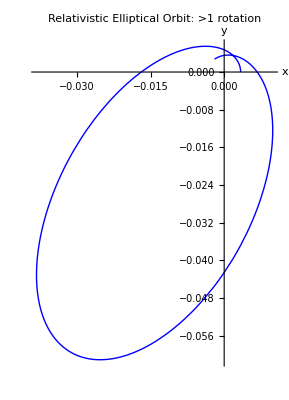

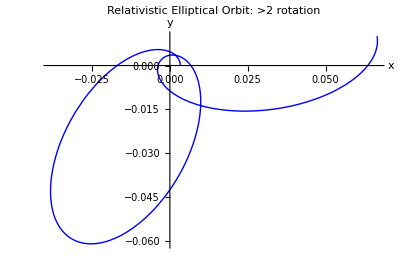

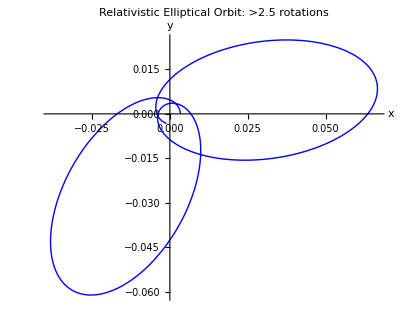

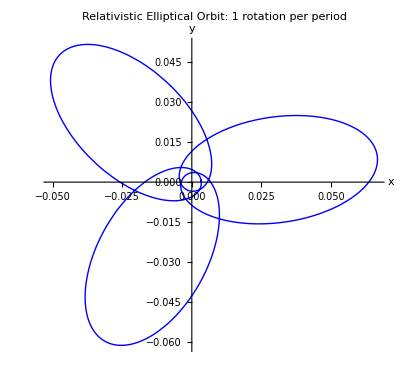

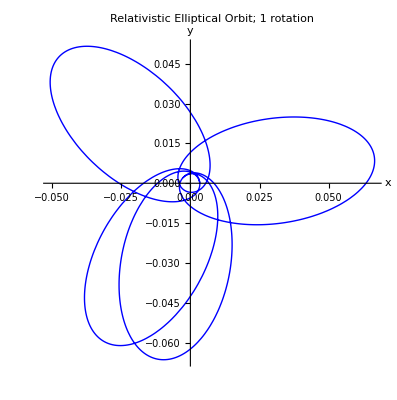

```mathematica
(*Physical constants*)
Z=92; (*Atomic number of Uranium, U*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal) //N
eVal=eFunc[ntVal,nrVal]//N
Z

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: >1 rotation",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue, Thick}]
PolarPlot[r[t],{t,0,1.5*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: >2 rotation",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue, Thick}]
PolarPlot[r[t],{t,0,2*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: >2.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,3*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: 1 rotation per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,4*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit; 1 rotation",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["UraniumIon91.pdf",%%]
```

UraniumIon91.pdf

```mathematica
r[t]
```

0.0063989/(1+0.904882 Cos[0.741135 t])

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,2*4*PeriodTheta,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Uranium, U, when Z=92, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω=0.741135,  ϵ=0.904882, and a=0.0353163, in Bohr’s atomic units. 
The perihelion and aphelion move along two concentric circles around the nucleus with radii:  r_min=a (1-ϵ)=0.003359209 and r_max=a (1+ϵ)=0.067273472, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
CCW Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=2.19461.  ‘Winding’ number is one.

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.741135,0.904882,0.0353163}

```mathematica
{rMin, rMax}
```

{0.00335921,0.0672735}

```mathematica
{DeltaTheta,PeriodTheta}
```

{2.19461,8.47779}

```mathematica
{eVal,Z,ntVal,nrVal}
```

{0.933042,92,1,1}

```mathematica
r[t]
```

0.0063989/(1+0.904882 Cos[0.741135 t])

(*End of Uranium, Z=92, section*)

## Copernicium, Cn, Z=122

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.576207

0.930786

0.0249872

{0.00172947,0.0482449}

4.6212

10.9044

0.887752

112

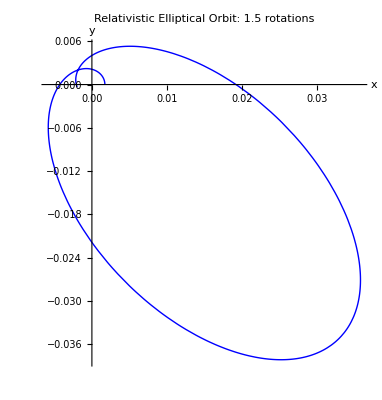

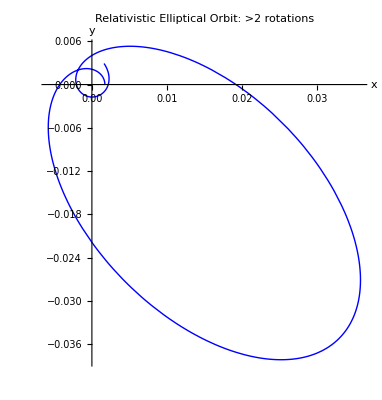

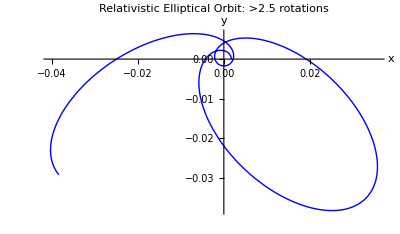

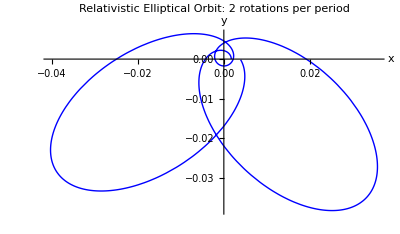

```mathematica
(*Physical constants*)
Z=112; (*Atomic number of Copernicium,Cn*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N
eVal=eFunc[ntVal,nrVal]//N
Z

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.88*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.25*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: >2 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.5*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: >2.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.725*PeriodTheta},PlotLabel->"Relativistic Elliptical Orbit: 2 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["CoperniciumIon111.pdf",%]
```

CoperniciumIon111.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,6*1.725*PeriodTheta,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Copernicium, Cn, when Z=112, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.576207,  ϵ=0.930786, and a=0.0249872, in Bohr’s atomic units. 
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.00172947 and r_max=a (1+ϵ)=0.0482449, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity. ‘Winding number is two.
CW Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=4.6212.  At the point of self-intersection one gets, approximately,  r[2.3799243523877007`]=r[8.52445631673413`]=0.00281928 with  r[2.3799243523877007`]-r[8.52445631673413`]=-1.73472×10^-18.

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.576207,0.930786,0.0249872}

```mathematica
{rMin, rMax}
```

{0.00172947,0.0482449}

```mathematica
{DeltaTheta,PeriodTheta}
```

{4.6212,10.9044}

```mathematica
{eVal,Z,ntVal,nrVal}
```

{0.887752,112,1,1}

```mathematica
r[t]
```

0.00333924/(1+0.930786 Cos[0.576207 t])

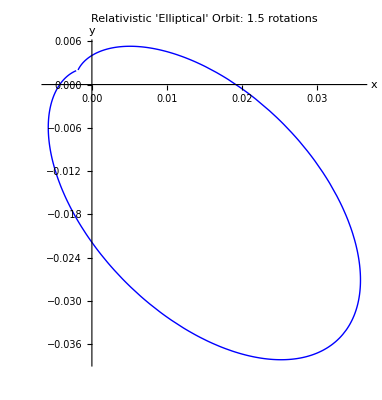

```mathematica
PolarPlot[r[t],{t,0.22*PeriodTheta,0.788*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
{0.22*PeriodTheta,0.788*PeriodTheta}
```

{2.39896,8.59265}

```mathematica
r[2.398963747206803]-r[8.592651967268004]
```

0.000106539

```mathematica
8.592651967268004/2.398963747206803
```

3.58182

```mathematica
FindRoot[r[t]-r[3.5818181818181825*t]==0,{t,2.4}]
```

{t→2.37992}

```mathematica
3.5818181818181825*2.3799243523877007
```

8.52446

```mathematica
r[2.3799243523877007]-r[8.52445631673413]
```

-1.73472×10^-18

```mathematica
{r[2.3799243523877007],r[8.52445631673413]}
```

{0.00281928,0.00281928}

```mathematica
3.1415926535897927-Pi//N
```

-4.44089×10^-16

(*End of Copernicium, Cn, Z=112, section*)

## Oganesson, Og, Z=118

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.508457

0.941479

0.0222041

{0.0012994,0.0431087}

6.07418

12.3574

0.868463

118

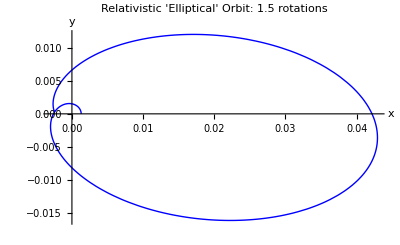

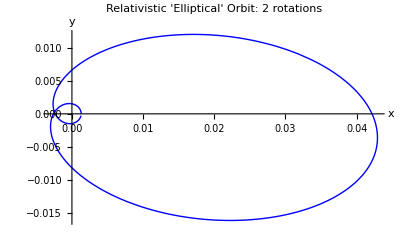

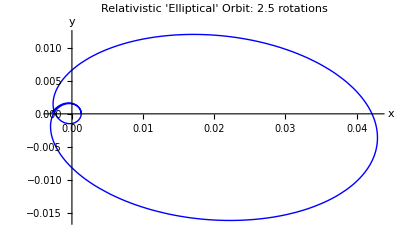

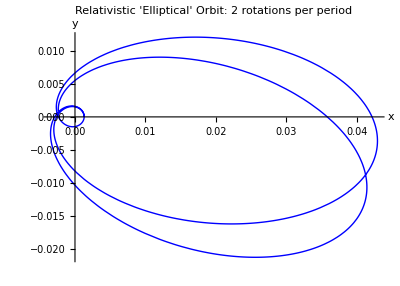

```mathematica
(*Physical constants*)
Z=118; (*Atomic number of Oganesson, Og*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N
eVal=eFunc[ntVal,nrVal]//N
Z

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.75*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.269*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.75*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["OganessonIon117.pdf",%]
```

OganessonIon117.pdf

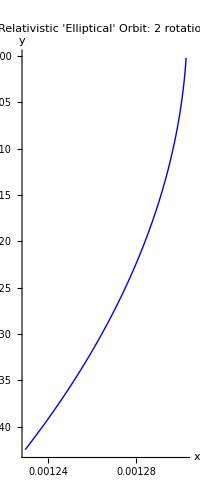

```mathematica
(* the loop *)PolarPlot[r[t],{t,0.99*PeriodTheta,1.01679*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
1.01679*PeriodTheta
```

12.5648

```mathematica
{r[12.564847324276567]-r[0],r[1.01679*PeriodTheta]-r[0]}
```

{3.51253×10^-6,3.51253×10^-6}

```mathematica
FindRoot[r[t*1.01679*PeriodTheta]-r[0]==0,{t,1}]
```

{t→0.983487}

```mathematica
0.9834872651822683*1.01679*PeriodTheta
```

12.3574

```mathematica
r[12.357367332385502]-r[0]
```

3.25261×10^-18

```mathematica
(*Animation in Cartesian Coordinates: the first two rotations per period, twice*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic 'Elliptical Orbit'(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min]=0.001299 to Subscript[r, max]=0.0431087*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,2*1.75*PeriodTheta,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Oganesson ion, Og, when Z=118, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω=0.508457,  ϵ=0.941479, and a=0.0222041, in Bohr’s atomic units. 
The perihelion and aphelion move along two concentric circles around the nucleus with radii:  r_min=a (1-ϵ)=0.0012994 and r_max=a (1+ϵ)=0.043108700, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity. ‘Winding’ number is two.
CW Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=6.07418.  At the point of self-intersection one gets, approximately,  r[3.074037420536865]=r[9.283329709624294]=0.0025044 with  r[9.283329709624294`]-r[3.074037420536865`]=4.33681×10^-19.

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.508457,0.941479,0.0222041}

```mathematica
{rMin, rMax}
```

{0.0012994,0.0431087}

```mathematica
{DeltaTheta,PeriodTheta}
```

{6.07418,12.3574}

```mathematica
{eVal,Z,ntVal,nrVal}
```

{0.868463,118,1,1}

```mathematica
(* points of self-intersection *)r[9.283329709624294]-r[3.074037420536865]
```

4.33681×10^-19

```mathematica
{r[9.283329709624294],r[3.074037420536865]}
```

{0.0025044,0.0025044}

```mathematica
ωVal*(9.283329709624294+3.074037420536865)/2//N
```

3.14159

```mathematica
3.141592653589793-Pi//N
```

0.

```mathematica
r0[t_]:=0.004308954533019283
```

```mathematica
r[t_]:=0.0025227511535937256/(1+0.9414793136551063 Cos[0.5084566348962754 t])
```

```mathematica
{r0[t], r[t]}
```

{0.00430895,0.00252275/(1+0.941479 Cos[0.508457 t])}

```mathematica
PeriodTheta
```

12.3574

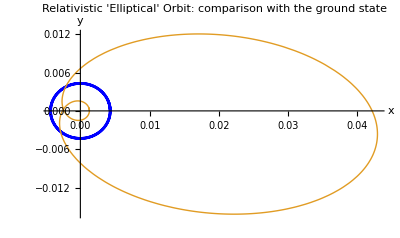

```mathematica
PolarPlot[{r0[t], r[t]},{t,0,1.05*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: comparison with the ground state",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue, Thick}]
```

```mathematica
Export["OganessonIon117SP.pdf",%]
```

OganessonIon117SP.pdf

(*End of Oganesson, Og,  Z=112, section*)

## Unbibium, Ubb, Z=122

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.455419

0.949782

0.0203534

{0.00102211,0.0396847}

7.5133

13.7965

0.853059

122

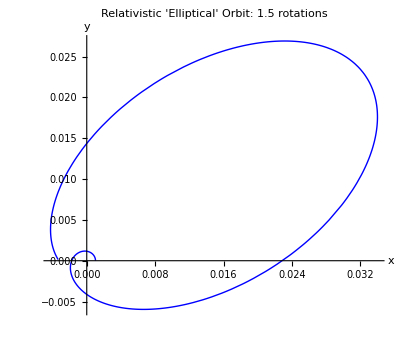

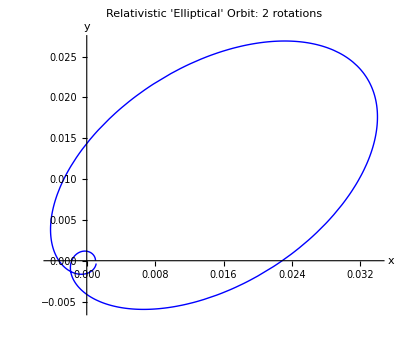

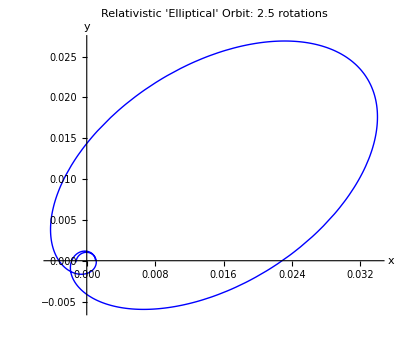

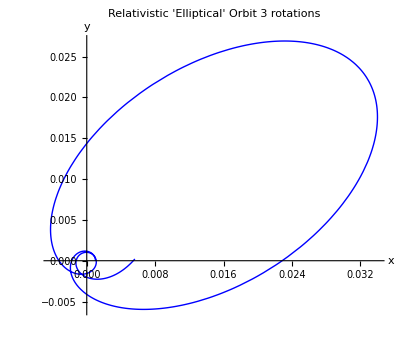

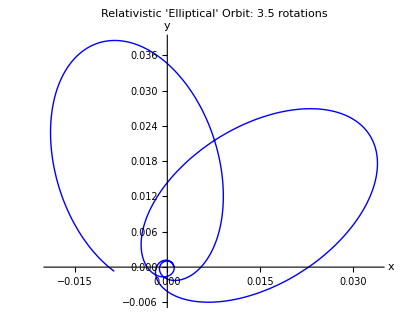

```mathematica
(*Physical constants*)
Z=122; (*Atomic number of a hypotetical element Unbibium, Ubb*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N
eVal=eFunc[ntVal,nrVal]//N
Z

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.68*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
 PolarPlot[r[t],{t,0,0.889*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.15*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.369*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit 3 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.6*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["UnbibiumIon121.pdf",%%]
```

UnbibiumIon121.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic 'Elliptical' Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,4*0.725*PeriodTheta,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Unbibium, Ubb, when Z=122, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.455419,  ϵ=0.949782, and a=0.0203534, in Bohr’s atomic units.  The ‘winding’ number is 3!
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.00102211 and r_max=a (1+ϵ)=0.0396847, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity. ‘Winding’ number is three.
CCW Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=7.5133.  
At the point of the first self-intersection one gets, approximately,  r(10.002448573515926)=r(3.7940322175405243)=0.00234067  with  r(10.002448573515926)-r(3.7940322175405243)=0. At the second self-intersection, approximately, r[(6.9329615821129)=r(10.66)=0.0017562 with

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.455419,0.949782,0.0203534}

```mathematica
{rMin, rMax}
```

{0.00102211,0.0396847}

```mathematica
{DeltaTheta,PeriodTheta}
```

{7.5133,13.7965}

```mathematica
{eVal,Z,ntVal,nrVal}
```

{0.853059,122,1,1}

```mathematica
(* Start of evaluating of self-intersections: *)0.725*PeriodTheta
```

10.0024

```mathematica
r[10.002448573515926]
```

0.00234067

```mathematica
Solve[ωVal*(10.002448573515926+t)/2-Pi==0,t]
```

{{t→3.79403}}

```mathematica
r[3.794032217540524]
```

0.00234067

```mathematica
10.002448573515926/3.794032217540524
```

2.63636

```mathematica
FindRoot[r[2.636363636363636*t]-r[t],{t,3.7}]
```

{t→3.79403}

```mathematica
2.636363636363636*3.7940322175405243
```

10.0024

```mathematica
r[10.002448573515926]-r[3.7940322175405243]
```

0.

```mathematica
{r[10.002448573515926],r[3.7940322175405243]}
```

{0.00234067,0.00234067}

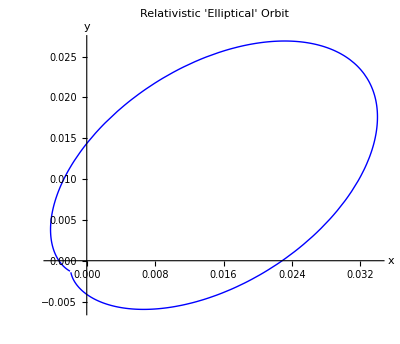

```mathematica
PolarPlot[r[t],{t,3.7940322175405243,10.002448573515926},PlotLabel->"Relativistic 'Elliptical' Orbit",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Solve[ωVal*(10.66+t)/2-2*Pi==0,t]
```

{{t→16.933}}

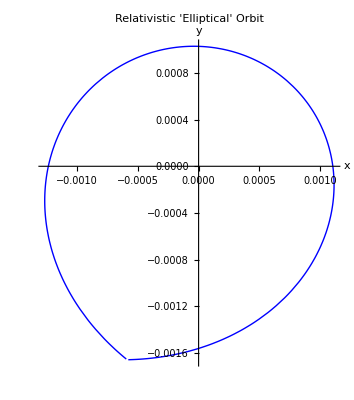

```mathematica
PolarPlot[r[t],{t,10.66, 16.9329615821129},PlotLabel->"Relativistic 'Elliptical' Orbit",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
r[16.932961582112902]-r[10.660000000000002]
```

1.51788×10^-18

```mathematica
16.932961582112902/10.660000000000002
```

1.58846

```mathematica
FindRoot[r[1.588457934532167*t]-r[t]==0,{t,10}]
```

{t→10.66}

```mathematica
1.588457934532167*10.66
```

16.933

```mathematica
r[16.9329615821129]-r[10.660000000000002]
```

-8.67362×10^-19

```mathematica
16.9329615821129/10.660000000000002
```

1.58846

```mathematica
FindRoot[r[1.5884579345321665*t]-r[t]==0,{t,10.6}]
```

{t→10.66}

```mathematica
1.5884579345321665*10.660000000000002
```

16.933

```mathematica
r[16.9329615821129]-r[10.660000000000002]
```

-8.67362×10^-19

```mathematica
{r[16.9329615821129],r[10.660000000000002]}
```

{0.0017562,0.0017562}

(*End of Unbibium, Ubb,  Z=122, section*)

## Unbiennium, Ube, Z=129

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.337408

0.967653

0.0169559

{0.000548474,0.0333634}

12.3387

18.6219

0.817743

129

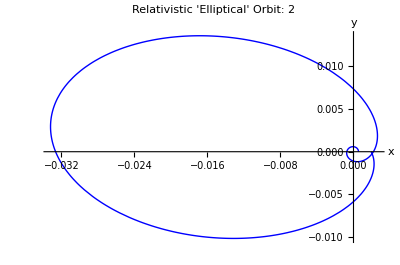

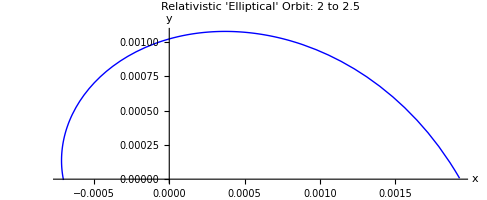

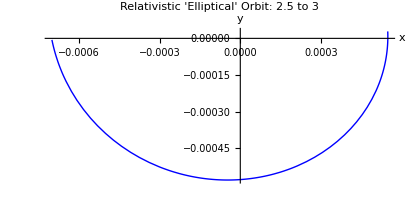

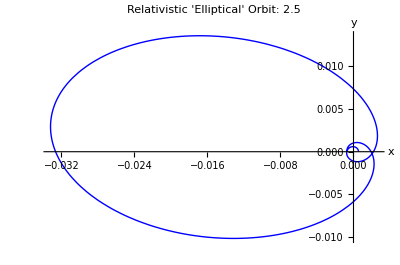

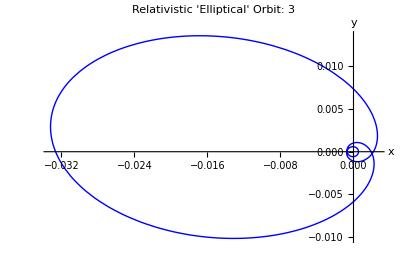

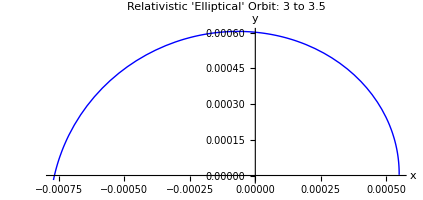

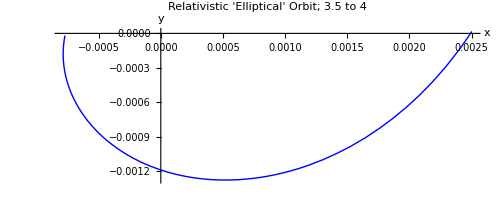

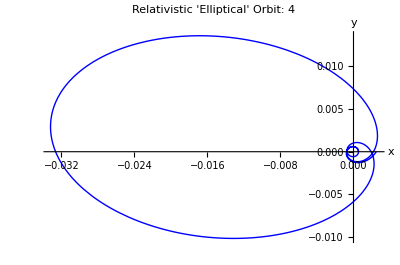

```mathematica
(*Physical constants*)
Z=129; (*Atomic number number 129 is assigned for a hypothetical undiscovered element temporarily named Unbiennium, Ube*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N
eVal=eFunc[ntVal,nrVal]//N
Z

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.675*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.675*PeriodTheta, 0.844*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 to 2.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.844*PeriodTheta, 1.015*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5 to 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.844*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.0125*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,1.0125*PeriodTheta,1.18225*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3 to 3.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,1.182225*PeriodTheta, 1.35*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit; 3.5 to 4",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0, 1.35*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0, 1.5*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["UnbienniumIon128.pdf",%]
```

UnbienniumIon128.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,4*1.5*PeriodTheta,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in a hypothetical hydrogen-like ion of Unbiseptium, Ube, when Z=129, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.337408,  ϵ=0.967653, and a=0.0169559, in Bohr’s atomic units. The ‘winding number’ is four.
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)= 0.000548474 and r_max=a (1+ϵ)=0.0333634, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
CW Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=12.3387.

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.337408,0.967653,0.0169559}

```mathematica
{rMin, rMax}
```

{0.000548474,0.0333634}

```mathematica
{DeltaTheta,PeriodTheta}
```

{12.3387,18.6219}

```mathematica
{eVal,Z,ntVal,nrVal}
```

{0.817743,129,1,1}

(*End of Unbiseptium, Ube, Z=129, section*)

## Untribium, Utb, Z=132

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.268605

0.977328

0.0153084

{0.000347077,0.0302698}

17.1088

23.392

0.796431

132

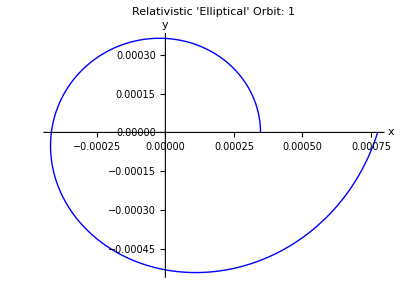

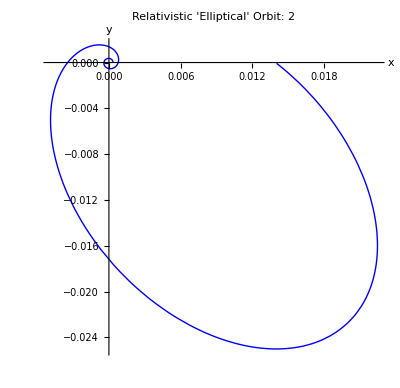

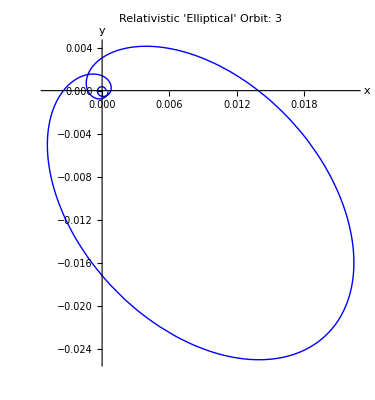

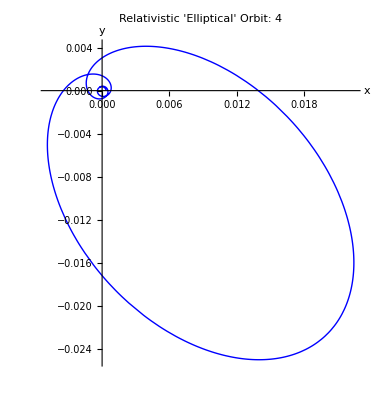

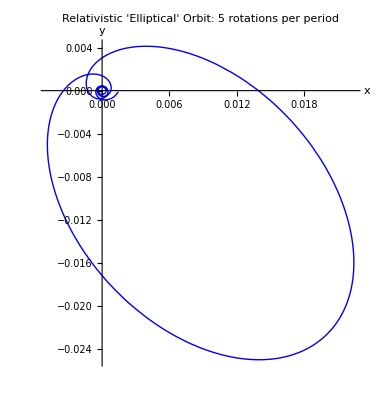

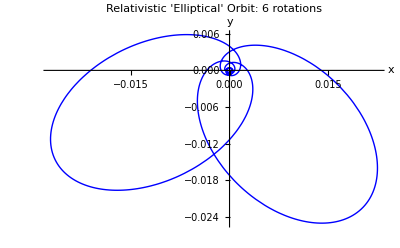

```mathematica
(*Physical constants*)
Z=132; (*Atomic number number 132 is assigned for a hypothetical undiscovered element temporarily named Untribium, Utb*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N
eVal=eFunc[ntVal,nrVal]//N
Z

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.2685*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.537*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.8*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.9*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.34*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,1.75*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["UntribiumIon131.pdf",%%]
```

UntribiumIon131.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,24 Pi,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in a hypothetical hydrogen-like ion of Untribium, Utb, when Z=132, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.268605,  ϵ=0.977328, and a=0.0153084, in Bohr’s atomic units. The ‘winding number’ is five.
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.000347077 and r_max=a (1+ϵ)=0.0302698, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=17.1088.

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.268605,0.977328,0.0153084}

```mathematica
{rMin, rMax}
```

{0.000347077,0.0302698}

```mathematica
{DeltaTheta,PeriodTheta,Z}
```

{17.1088,23.392,132}

```mathematica
{eVal,Z, ntVal, nrVal}
```

{0.796431,132,1,1}

(*End of Untribium, Utb, Z=132, section*)

## Untripentium, Utp, Z=135

```mathematica
Clear[ntVal,nrVal,ωVal,aVal,rMin,rMax,Z,DeltaTheta, PeriodTheta, eVal]
```

0.171738

0.989201

0.013287

{0.00014349,0.0264305}

30.3026

36.5858

0.765421

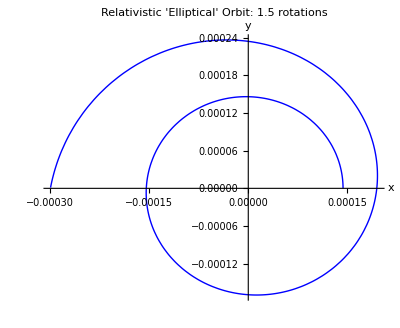

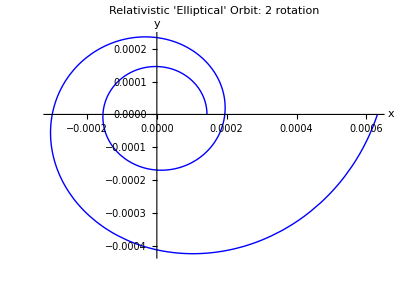

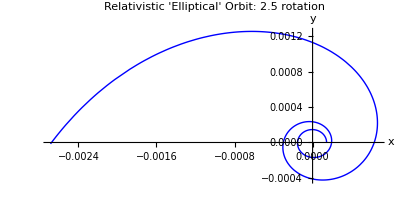

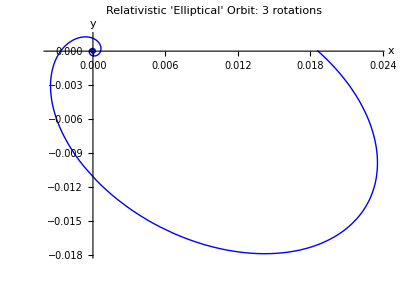

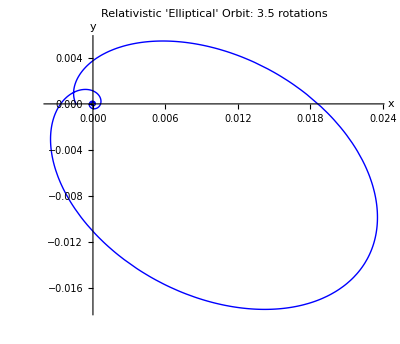

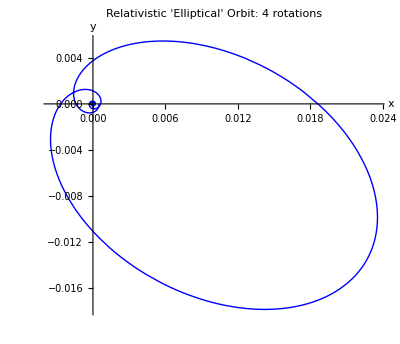

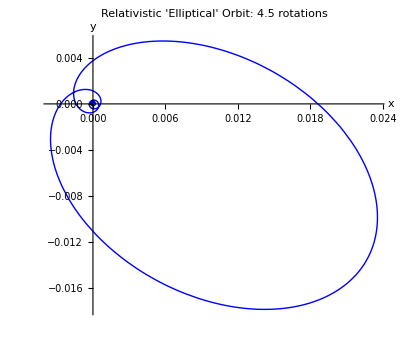

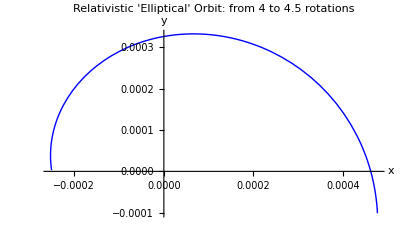

```mathematica
(*Physical constants*)
Z=135; (*Atomic number number 135 is assigned for a hypothetical undiscovered element temporarily named Untripentium, Utp*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N
eVal=eFunc[ntVal,nrVal]//N

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.2575*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.3435*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotation",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.4295*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5 rotation",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.5153*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.6025*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 3.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.685*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.7725*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 4.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.68123*PeriodTheta, 0.7725*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: from 4 to 4.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.8585*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.7725*PeriodTheta,0.8585*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: from 4.5 to 5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.9*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.8585*PeriodTheta,0.94447*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: from 5 to 5.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0,0.94447*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.94447*PeriodTheta, 1.2022*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: from 5.5 to 6 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0, 1.2022*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0.94447*PeriodTheta, 1.288*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 5.5 to 6.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0, 1.29*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6.5 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,1.287*PeriodTheta, 1.547*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: from 6.5 to 7 rotations",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
PolarPlot[r[t],{t,0, 1.547*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 6 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Blue,Thick}]
```

```mathematica
Export["UntripentiumIon134.pdf",%]
```

UntripentiumIon134.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic Elliptical Orbit(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min] to Subscript[r, max]*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,4*1.547*PeriodTheta,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in a hypothetical hydrogen-like ion of Untripentium, Utp, when Z=135 and the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω= 0.171738,  ϵ=0.989201, and a=0.013287, in Bohr’s atomic units. The ‘winding number’ is about 6.
The perihelion and aphelion move along two concentric circles around the nucleus with radii:   r_min=a (1-ϵ)=0.00014349 and r_max=a (1+ϵ)=0.0264305, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
CCW Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=30.3026.

Verification:

```mathematica
{ωVal, ϵVal, aVal}
```

{0.171738,0.989201,0.013287}

```mathematica
{rMin, rMax}
```

{0.00014349,0.0264305}

```mathematica
{DeltaTheta,PeriodTheta}
```

{30.3026,36.5858}

```mathematica
{eVal,Z,ntVal,nrVal}
```

{0.765421,135,1,1}

(*End of Untripentium, Utp, when Z=135, section*)

(*End of notebook*)